# FeynCalc Utilities

## Load FeynCalc

```mathematica
$LoadAddOns={"FeynHelpers","FeynArts"};
<<FeynCalc`;
$FAVerbose=False;
FAPatch[PatchModelsOnly->True]
```

## Particles

```mathematica
(*determine if state is a fermion*)
IsFermion[state_]:=Module[{head},
(*if state looks like: -F[1], need to strip off the `Times` head *)head=If[Head[state]===Times,Head[ReplaceAll[state,Times[a_,b__]:>b]],Head[state]];
head===FeynArts`F||head===FeynArts`U
];

(*determine if state is a vector*)

IsVector[state_]:=Module[{head},
(*if state looks like: -V[1], need to strip off the `Times` head*)head=If[Head[state]===Times,Head[ReplaceAll[state,Times[a_,b__]:>b]],Head[state]];
head===FeynArts`V
];
```

## Substitute Unstable Propagator

```mathematica
GetWidth[SMP["m_H"]|MH]=ΓH;
GetWidth[SMP["m_Z"]|MZ]=ΓZ;
GetWidth[SMP["m_W"]|MW]=ΓW;
GetWidth[MSM]=ΓSM;

SubstituteUnstablePropagator[expr_]:=expr/.{
FeynAmpDenominator[PropagatorDenominator[Momentum[a__],m:SMP["m_H"]|MH|SMP["m_Z"]|MZ|SMP["m_W"]|MW|MSM]]:>Den[ScalarProductExpand[SP[a,a]]-m^2+I*GetWidth[m]*m]
}
Den/:Times[Den[a__],Den[b__]]:=Den[a*b]
```

## Correction Final Expression

```mathematica
CorrectParameters[expr_]:=expr/.{
SMP["m_H"]->MH,
SMP["m_W"]->MW,
SMP["m_Z"]->MZ,
SMP["m_t"]->MTOP,
SMP["m_b"]->MB,
SMP["e"]->√(4π alphaEM),

FCGV["MH"]->MH,
FCGV["MZ"]->MZ,
FCGV["MW"]->MW,
FCGV["MT"]->MTOP,
FCGV["MB"]->MB,

FCGV["EL"]->√(4π alphaEM),
Plus[cw^2,sw^2]:>1,
SUNFDelta[SUNFIndex[a_],SUNFIndex[b_]]^2:>Ncol
}
```

## Generating Diagrams

```mathematica
Options[GenerateDiagrams]={
(* CreateTopologies Options *)
LoopNumber->0,
Adjacencies->OptionValue[CreateTopologies,Adjacencies],
ExcludeTopologies->OptionValue[CreateTopologies,ExcludeTopologies],
(* InsertFields Options *)
ExcludeParticles->OptionValue[InsertFields,ExcludeParticles],
InsertionLevel->{Particles},
Model->OptionValue[InsertFields,Model],
GenericModel->OptionValue[InsertFields,GenericModel],
(* Painting Options *)
Paint->False,
ColumnsXRows->OptionValue[Paint,ColumnsXRows],
(* Custom options *)
DiagramExtract->None
};
```

```mathematica
GenerateDiagrams[inStates_List->outStates_List,OptionsPattern[]]:=Module[{topologies,diagrams},
(* Create the topologies *)
topologies=CreateTopologies[
OptionValue[LoopNumber],
Length[inStates]->Length[outStates],
ExcludeTopologies->OptionValue[ExcludeTopologies],
Adjacencies->OptionValue[Adjacencies]
];
(* Generate the diagrams *)
diagrams=InsertFields[
topologies,
inStates->outStates,
InsertionLevel->OptionValue[InsertionLevel],
ExcludeParticles->OptionValue[ExcludeParticles],
Model->OptionValue[Model],
GenericModel->OptionValue[GenericModel]
];
If[Not[SameQ[OptionValue[DiagramExtract],None]],diagrams=DiagramExtract[diagrams,OptionValue[DiagramExtract]]];
(* Paint if requested *)
If[OptionValue[Paint],
Paint[diagrams,ColumnsXRows->OptionValue[ColumnsXRows]];
];
diagrams
]
```

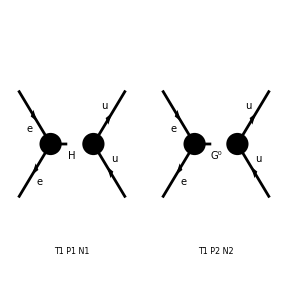

```mathematica
(*
GenerateDiagrams[{F[2,{1}],-F[2,{1}]}->{F[3,{1}],-F[3,{1}]},Paint->True,InsertionLevel->{Particles},DiagramExtract->{1,2}];
*)
```

## Creating Amplitudes

```mathematica
Options[ComputeAmplitude]=Join[
Options[GenerateDiagrams],
Options[CreateFeynAmp],
Options[FCFAConvert]
];

ComputeAmplitude[inStates_List->outStates_List,OptionsPattern[]]:=Module[{diagrams,ampFA,ampFC},
ClearScalarProducts[];
diagrams=GenerateDiagrams[
inStates->outStates,
LoopNumber->OptionValue[LoopNumber],
Adjacencies->OptionValue[Adjacencies],
ExcludeTopologies->OptionValue[ExcludeTopologies],
ExcludeParticles->OptionValue[ExcludeParticles],
InsertionLevel->OptionValue[InsertionLevel],
Model->OptionValue[Model],
GenericModel->OptionValue[GenericModel],
Paint->OptionValue[Paint],
ColumnsXRows->OptionValue[ColumnsXRows],
DiagramExtract->OptionValue[DiagramExtract]
];

ampFA=CreateFeynAmp[
diagrams,
AmplitudeLevel->OptionValue[AmplitudeLevel],
GaugeRules->OptionValue[GaugeRules],
PreFactor->OptionValue[PreFactor],
Truncated->OptionValue[Truncated],
MomentumConservation->OptionValue[MomentumConservation],
GraphInfoFunction->OptionValue[GraphInfoFunction]
];

ampFC=FCFAConvert[
ampFA,
ChangeDimension->OptionValue[ChangeDimension],
Contract->OptionValue[Contract],
DropSumOver->OptionValue[DropSumOver],
FCFADiracChainJoin->OptionValue[FCFADiracChainJoin],
FeynAmpDenominatorCombine->OptionValue[FeynAmpDenominatorCombine],
FinalSubstitutions->OptionValue[FinalSubstitutions],
IncomingMomenta->OptionValue[IncomingMomenta],
List->OptionValue[List],
LoopMomenta->OptionValue[LoopMomenta],
LorentzIndexNames->OptionValue[LorentzIndexNames],
OutgoingMomenta->OptionValue[OutgoingMomenta],
Prefactor->OptionValue[Prefactor],
SMP->OptionValue[SMP],
SUNFIndexNames->OptionValue[SUNFIndexNames],
SUNIndexNames->OptionValue[SUNIndexNames],
TransversePolarizationVectors->OptionValue[TransversePolarizationVectors],
UndoChiralSplittings->OptionValue[UndoChiralSplittings]
];


ampFC=Map[
Simplify[
ExpandScalarProduct[
DiracSimplify[
Contract[
SubstituteUnstablePropagator[
ReplaceAll[#,
{FALeviCivita->Eps,FAFourVector->Momentum}
]
]
],DiracSubstitute67->True]
]
]&,ampFC]
]
```

```mathematica
(*
ComputeAmplitude[{F[1,{1}],-F[1,{1}]}->{V[1],V[1]},Model->"QED",Paint->True,ColumnsXRows->{2,1},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},SMP->True,TransversePolarizationVectors->{k1,k2},DiagramExtract->{1},List->False]
*)
```

## Creating Squared Amplitudes

```mathematica
Options[ComputeAmplitudeSquared]=Options[ComputeAmplitude];
```

```mathematica
ComputeAmplitudeSquared[inStates_List->outStates_List,opts:OptionsPattern[]]:=Module[{iAmp,iIncomingMomenta,iOutgoingMomenta,iIter,iMsqrd,iDoFermionSpinSum,iFermionSpinSumPreFactor,
iDoPolarizationSum,iPolarizationSumPreFactor,iPolarizationSumStateMomenta
},
iAmp=ComputeAmplitude[inStates->outStates,opts];
ClearScalarProducts[];

(* Determine incoming/outogoing momenta *)
iIncomingMomenta=OptionValue[IncomingMomenta];
iOutgoingMomenta=OptionValue[OutgoingMomenta];
(* 
If user didn't specify momenta, populate them
based on what FeynCalc does
*)
For[iIter=Length[iIncomingMomenta]+1,iIter≤Length[inStates],iIter++,
AppendTo[iIncomingMomenta,ToExpression["InMom"<>ToString[iIter]]];
];
For[iIter=Length[iOutgoingMomenta]+1,iIter≤Length[outStates],iIter++,
AppendTo[iOutgoingMomenta,ToExpression["OutMom"<>ToString[iIter]]];
];

(* Set the masses *)
For[iIter=1,iIter≤Length[iIncomingMomenta],iIter++,
SP[iIncomingMomenta[[iIter]]]=TheMass[inStates[[iIter]]]^2;
];
For[iIter=1,iIter≤Length[iOutgoingMomenta],iIter++,
SP[iOutgoingMomenta[[iIter]]]=TheMass[outStates[[iIter]]]^2;
];

(*Square Amplitude *)
If[OptionValue[List]==True,
(* Diagonal *)
iMsqrd=Table[iAmp⟦i⟧*ComplexConjugate[iAmp⟦i⟧],{i,Length[iAmp]}];
(* Off diagonals *)
iMsqrd=Join[iMsqrd,Flatten[Table[iAmp⟦i⟧*ComplexConjugate[iAmp⟦j⟧],{i,1,Length[iAmp]-1},{j,i+1,Length[iAmp]}]]];,
iMsqrd = iAmp*ComplexConjugate[iAmp];
];

(* If any of the states are fermionic, average their spins *)
iFermionSpinSumPreFactor=Times@@Map[If[IsFermion[#],1/2,1]&,inStates];
iDoFermionSpinSum=AnyTrue[Join[inStates,outStates],IsFermion];
If[
iDoFermionSpinSum,
If[OptionValue[List]==True,
iMsqrd=Map[ReplaceAll[FermionSpinSum[#,ExtraFactor->iFermionSpinSumPreFactor],DiracTrace->TR]&,iMsqrd];,
iMsqrd=FermionSpinSum[iMsqrd,ExtraFactor->iFermionSpinSumPreFactor]/.DiracTrace->TR;
];
];

(* If any of the states are vectors, average polarizations *)
(*Determine if polarization sum needs to be performed *)
iDoPolarizationSum=AnyTrue[Join[inStates,outStates],IsVector];
(* Determine the prefactor *)
iPolarizationSumPreFactor=Times@@Map[If[IsVector[#],If[TheMass[#]===0,1/2,1/3],1]&,inStates];
(* Determine the momenta we need to do polarization sums over *)
iPolarizationSumStateMomenta=Cases[
MapThread[List[#1,#2]&,{Join[inStates,outStates],Join[iIncomingMomenta,iOutgoingMomenta]}],{c_.V[_],_}
];
iMsqrd=iPolarizationSumPreFactor*iMsqrd;
If[iDoPolarizationSum,
For[iIter=1,iIter≤Length[iPolarizationSumStateMomenta],iIter++,
If[TheMass[iPolarizationSumStateMomenta[[iIter,1]]]===0,
iMsqrd=If[OptionValue[List]==True,
Map[DoPolarizationSums[#,iPolarizationSumStateMomenta[[iIter,2]],0]&,iMsqrd],
DoPolarizationSums[iMsqrd,iPolarizationSumStateMomenta[[iIter,2]],0]
];,
iMsqrd=If[OptionValue[List]==True,
Map[DoPolarizationSums[#,iPolarizationSumStateMomenta[[iIter,2]]]&,iMsqrd],
DoPolarizationSums[iMsqrd,iPolarizationSumStateMomenta[[iIter,2]]]
];
];
];
];

If[OptionValue[List]==True,
iMsqrd=Map[ReplaceAll[#,Den[a_]:>1/a]&,iMsqrd];
iMsqrd=Map[Simplify[Contract[#]]&,iMsqrd];
ClearScalarProducts[];
Return[Map[CorrectParameters,iMsqrd]];,

iMsqrd=Collect[Contract[iMsqrd],Den[__],Simplify];
ClearScalarProducts[];
Return[CorrectParameters[iMsqrd]];
];
]
```

```mathematica
(*
Module[{msqrd,σEEtoγγ,dσdzEEtoγγPeskin},
msqrd=ComputeAmplitudeSquared[{F[1,{1}],-F[1,{1}]}->{V[1],V[1]},Model->"QED",Paint->True,ColumnsXRows->{2,1},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},SMP->True,TransversePolarizationVectors->{k1,k2},SMP->True,DiagramExtract->{1}];
msqrd=msqrd/.{FCGV["ME"]->SMP["m_e"]};
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_e"],0,0];
Simplify[msqrd/.{u->2 SMP["m_e"]^2-s-t}]
]//InputForm
*)
```

## 2->2 Integration Table

```mathematica
(*CrossSection22IntegralTable[expr_,t_,tMin_,tMax_]:=FixedPoint[ReplaceAll[#,{
(c_. t^(n_.)+d_.)(x_.t+a_.)^(m_.):>( c/x^(n+1)Sum[Binomial[n,k](-a)^(n-k)Piecewise[{{((x*tMax+a)^(k+m+1)-(x*tMin+a)^(k+m+1))/(k+m+1),k+m≠-1},{Log[(x*tMax+a)/(x*tMin+a)],k+m==-1}}],{k,0,n}]+d(x t+a)^m)/;n>=0&&m<=0&&FreeQ[x,t]&&UnsameQ[x,0]&&UnsameQ[c,0],


(* Integrals of t^n/ X *)
(c_. t^(n_.)+d__)(x_.t+a_)^-1(y_.t+b_)^-1:>(c*((-a)^n/(x^n(b*x-a*y))(Log[(x*tMin+a)/(x*tMin+a)]+Sum[Binomial[n,k]/((-a)^k k)((x*tMax+a)^k-(x*tMin+a)^k),{k,1,n}])
+(-b)^n/(y^n(a*y-b*x))(Log[(y*tMax+b)/(y*tMin+b)]+Sum[Binomial[n,k]/((-b)^k k)((y*tMin+b)^k-(y*tMin+b)^k),{k,1,n}]))+d/((x t+a)(y t+b)))/;n>=0&&a/x=!=b/y&&FreeQ[x,t]&&UnsameQ[x,0]&&UnsameQ[y,0]&&UnsameQ[c,0],


c_.(x_.t+a_.)^(m_.):>( c/x Piecewise[{{((a+tMax*x)^(1+m)-(a+tMin*x)^(1+m))/(1+m),m≠-1},{Log[(a+tMax*x)/(a+tMin*x)],m==-1}}])/;m<=0&&FreeQ[x,t]&&UnsameQ[x,0]&&UnsameQ[c,0],


c_. t^(n_.):>1/(n+1)(tMax^(n+1)-tMin^(n+1))/;n=!=-1&&UnsameQ[c,0],


(c_.)/t:>Log[tMax/tMin]/;UnsameQ[c,0]
}]&,expr]*)
```

## 2->2 Cross Sections

```mathematica
Options[ComputeCrossSection22]=DeleteCases[Options[ComputeAmplitudeSquared],IncomingMomenta|OutgoingMomenta->__];
```

```mathematica
ComputeCrossSection22[{in1_,in2_}->{out1_,out2_},Q_,opt:OptionsPattern[]]:=Module[{iMsqrd,opts,iP1,iP2,iP3,iP4,iM1,iM2,iM3,iM4,iS,iT,iU,iE1,iE3,iPi,iPf,iPreFactor,iTMin,iTMax},
ClearScalarProducts[];
opts=Join[Flatten[List[opt]],{IncomingMomenta->{iP1,iP2},OutgoingMomenta->{iP3,iP4}}];

iMsqrd=ComputeAmplitudeSquared[{in1,in2}->{out1,out2},opts];

If[OptionValue[List]==True,
iMsqrd=ParallelMap[ReplaceAll[PropagatorDenominatorExplicit[#],{Den[a_]:>1/a}]&,iMsqrd];,
iMsqrd=PropagatorDenominatorExplicit[iMsqrd]/.Den[a__]:>1/a;
];
(* Extract masses *)
iM1 = FeynArts`TheMass[in1];
iM2 = FeynArts`TheMass[in2];
iM3 = FeynArts`TheMass[out1];
iM4 = FeynArts`TheMass[out2];

(* Set the Mandelstam variables*)
SetMandelstam[iS,iT,iU,iP1,iP2,-iP3,-iP4,iM1,iM2,iM3,iM4];

(* Remove u *)
If[OptionValue[List]==True,
iMsqrd=Map[Simplify[ReplaceAll[#,{iU->iM1^2+iM2^2+iM3^2+iM4^2-iS-iT}]]&,iMsqrd];,
iMsqrd=Simplify[iMsqrd]/.{iU->iM1^2+iM2^2+iM3^2+iM4^2-iS-iT};
];

(* Compute energies *)
iE1= (iS+ iM1^2 -iM2^2) / (2 * Sqrt[iS]);
iE3= (iS+ iM3^2 -iM4^2) / (2 * Sqrt[iS]);

(* Compute momenta *)
iPi = Sqrt[iE1^2-iM1^2];
iPf = Sqrt[iE3^2-iM3^2];

(* Compute cross section prefactor *)
iPreFactor=Simplify[(2π)/(64 π^2 Q^2)(iPf/iPi)*1/(2*iPi*iPf)];
(* if final states are identical, divide by 2 *)
If[out1===out2,iPreFactor=iPreFactor/2];

(* Compute bounds on t *)
iTMax = Simplify[iM1^2 + iM3^2 - 2iE1 * iE3 + 2 * iPi * iPf];
iTMin = Simplify[iM1^2 + iM3^2 - 2iE1 * iE3 - 2 * iPi * iPf];

(* Perform integration *)
If[OptionValue[List]==True,
Return[ParallelMap[ReplaceAll[iPreFactor*Integrate[CorrectParameters[#],{iT,iTMin,iTMax},GenerateConditions->False],iS->Q^2]&,iMsqrd]];,
Return[(iPreFactor*Integrate[CorrectParameters[iMsqrd],{iT,iTMin,iTMax},GenerateConditions->False])/.{iS->Q^2}];
]
];
```

```mathematica
(*
σ=ComputeCrossSection22[{F[1,{1}],-F[1,{1}]}->{V[1],V[1]},Q,Model->"QED",Paint->True,DiagramExtract->{2}]/.{FCGV["ME"]->SMP["m_e"],FCGV["EL"]->√(4π α)}//Simplify

*)
```

## Widths

```mathematica
Options[ComputeWidth]=DeleteCases[Options[ComputeAmplitudeSquared],IncomingMomenta|OutgoingMomenta->__];
```

```mathematica
ComputeWidth[{inState_}->{outState1_,outState2_}, opt:OptionsPattern[]] := Module[{msqrd, P, p1, p2, M, m1, m2, pf, preFactor, E1, E2,opts},
ClearScalarProducts[];
opts=Join[Flatten[List[opt]],{IncomingMomenta->{P},OutgoingMomenta->{p1,p2}}];

msqrd=PropagatorDenominatorExplicit[ComputeAmplitudeSquared[{inState}->{outState1,outState2},opts]]/.Den[a__]:>1/a;

M = FeynArts`TheMass[inState];
m1 = FeynArts`TheMass[outState1];
m2 = FeynArts`TheMass[outState2];

E1 = (M^2 + m1^2 - m2^2) / (2 * M);
E2 = (M^2 - m1^2 + m2^2) / (2 * M);

FeynCalc`SP[P, P] = M^2;
FeynCalc`SP[p1, p1] = m1^2;
FeynCalc`SP[p2, p2] = m2^2;
FeynCalc`SP[P, p1] = M * E1;
FeynCalc`SP[P, p2] = M * E2;
FeynCalc`SP[p1, p2] = (M^2 - m1^2 - m2^2) / 2;

msqrd = Simplify[msqrd];

pf = Sqrt[E1^2 - m1^2]; (* mag. of final state 3-momentum *)

preFactor = Simplify[(4 * π) / (2 * M) * pf / (16 * Pi^2 * M)];
(* If final state particles are identical, divide by 2 *)
preFactor *= If[outState1 ===outState2, 1 / 2, 1];
preFactor * msqrd
];
```